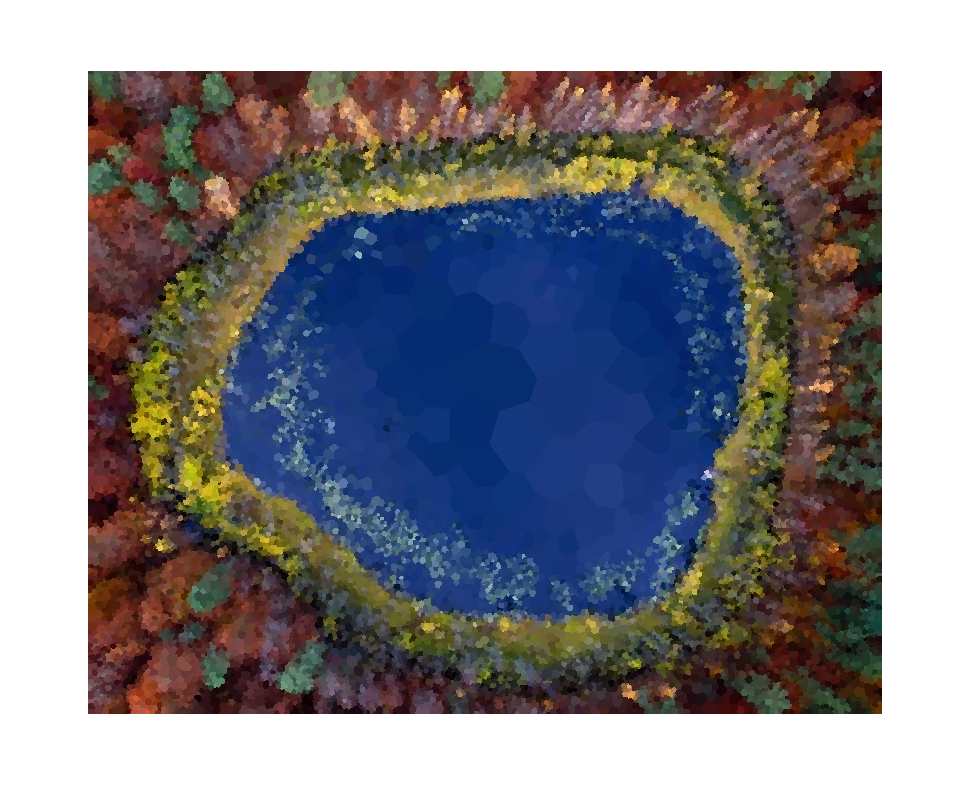

```mathematica
img=-Graphics-;
edges=EdgeDetect[img,5];
imgBounds=Transpose[{{0,0},ImageDimensions[img]}];
vm=VoronoiMesh[ImageValuePositions[edges,White],imgBounds];
vml=NestList[VoronoiMesh[Mean@@@MeshPrimitives[#,2],imgBounds]&,vm,3];
Graphics[Table[{RGBColor[ImageValue[img,Mean@@p]],p},{p,MeshPrimitives[Last[vml],2]}]]
```

```mathematica
NestList[VoronoiMesh[Mean@@@MeshPrimitives[#,2],imgBounds]&,vm,3];
```

```mathematica
polygons=Table[{RGBColor[ImageValue[img,Mean@@p]],p},{p,MeshPrimitives[Last[vml],2]}];
colors=polygons[[All,1]];
clusters=FindClusters[colors];
```

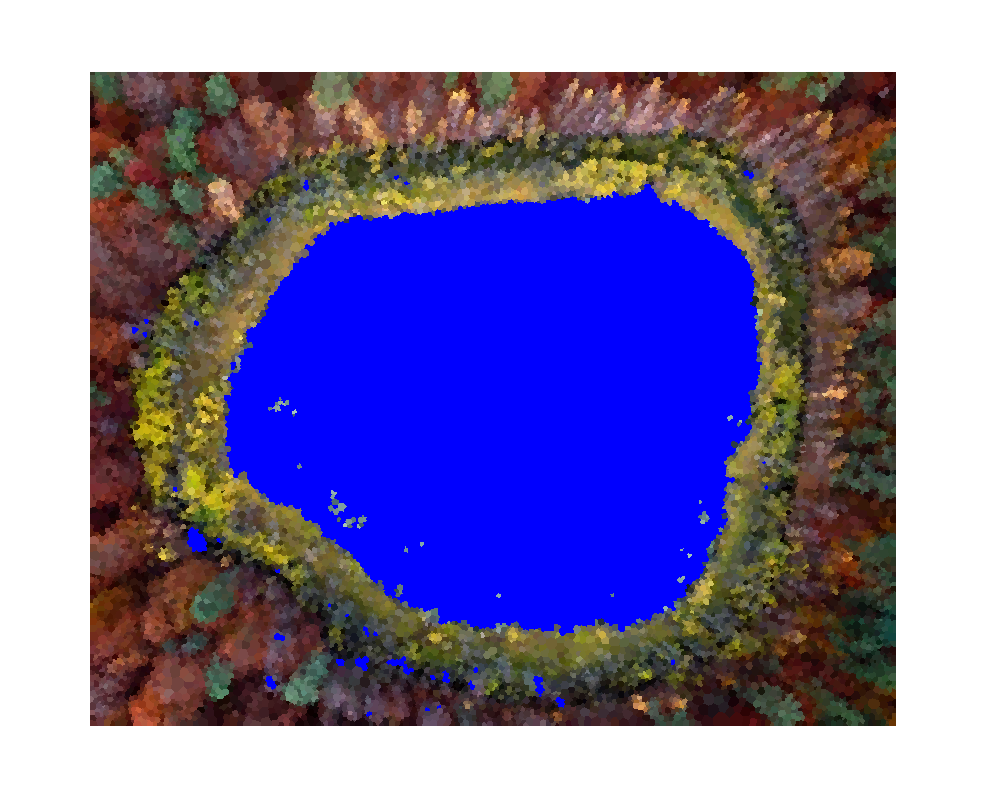

```mathematica
blue=clusters[[3]];
polygonsNew=If[MemberQ[blue,#[[1]]],{Blue,#[[2]]},#]&/@polygons;
Graphics[polygonsNew]
```